## Using Multilevel NAND trees to Create XOR Expressions

The goal of this project has been to explore NAND expressions and look for expressions equivalent to XOR. The Wolfram Language can already simplify XOR expressions with NANDs by using the following function but it only simplifies to a two level tree. By using more than two levels there is a possibility of finding a simpler version of three or four input XOR expressions. The reason that I chose to use NAND gates is that they are universal gates (any expression can be represented with a combination of NAND gates). Other universal gates like NOR would work but it seemed simplest to just stick with NAND to keep things consistent.

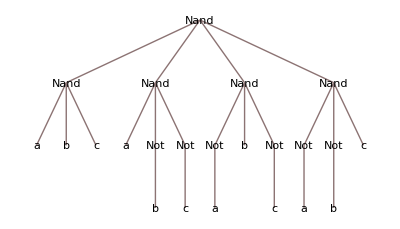

```mathematica
BooleanMinimize[Xor[a,b,c],"NAND"]//TreeForm
```

### Two Input Trees

The first thing that I tried was implementing a recursive function that keeps adding new layers of NAND gates.

```mathematica
Clear@nandTreeCreate;
```

```mathematica
nandTreeCreate[1] := DeleteCases[BooleanMinimize[Nand@@@Subsets[{a,b,c,!a,!b,!c},{2}],"Nand"],_Symbol]
```

```mathematica
nandTreeCreate[nGates_]:=Module[{},
DeleteCases[BooleanMinimize[Flatten[Table[Nand[x,#]&/@nandTreeCreate[nGates - 1],{x,{a,b,c,!a,!b,!c}}]],"NAND"],_Symbol]]
```

This turned out well except it only accounted for certain cases of two input trees. This is a very slim proportion of all of the different trees so a better computational method was required. The next function that I tried used the assumption that each NAND has a certain amount of NAND gates on each input. This makes it easy to go through all of the options recursively to until the branch reaches an end.

The code starts by defining the first case of the recursive function and then on the next gates it runs through the different combinations with tuples to generate all of the outcomes. It also creates NAND trees with half of the amount of NAND implemented and it doesn’t know what to do with an odd amount of gates so “nandTreeCreate” was implemented to fix that by multiplying the input by two.

```mathematica
Clear@nandTreeGenerate;
```

```mathematica
nandTreeGenerate[0]:={a,b,c,!a,!b,!c}
```

```mathematica
nandTreeGenerate[nGates_]:=Module[{subtrees = nandTreeGenerate/@Range[0,nGates-1]},
Join@@Table[Nand@@@Tuples[{subtrees[[i]],subtrees[[nGates-i]]}],{i,1,nGates-1}]
]
```

```mathematica
Clear@nandTreeCreate;
```

```mathematica
nandTreeCreate[nGates_]:=nandTreeGenerate[nGates*2]
```

This works super well at generating solutions but it’s very computationally intensive so the next step that I took was creating one that takes less processing power. This new version gets rid of duplicate cases by defining a new NAND function that returns null for trivial cases.

```mathematica
(*Example*) Xor[a,!a]
```

a⊻!a

It also creates a new version of tuples that uses this nand equation.

```mathematica
Clear@nand;
```

```mathematica
nand[a_,a_]:=Null;
nand[a_,!a_]:=Null;
nand[!a_,a_]:=Null;
nand[a_,b_]/;OrderedQ[{a,b}]:=Sow@Nand[a,b];
nand[a_,b_]:=Null;
```

```mathematica
Clear@nandTuples
```

```mathematica
nandTuples[list1_,list2_]:=Replace[Reap[Do[nand[a,b],{a,list1},{b,list2}]],{{_,{x_}}:>x,_:>{}}]
```

```mathematica
Clear@nandTreeGenerate
```

```mathematica
nandTreeGenerate[0]:={a,b,c,!a,!b,!c};
```

```mathematica
nandTreeGenerate[nGates_]:=nandTreeGenerate[nGates]=Module[{subtrees = nandTreeGenerate/@Range[0,nGates-1]},
Join@@Table[nandTuples[subtrees[[i]],subtrees[[nGates-i]]],{i,1,nGates-1}]
]
```

```mathematica
Clear@nandTreeCreate
```

```mathematica
nandTreeCreate[nGates_]:=nandTreeGenerate[nGates*2]
```

When testing my code I used the following function to compare the outputs to XOR

```mathematica
Select[nandTreeCreate[2],TautologyQ[Equivalent[Xor[a,b,c],#]]&]
```

{}

### Multi-Input Tree Generation

By inputting the amount of leaves into the recursive function, I was able to expand it in order to account for more than two input NAND gates. This uses the same general structure as the two input NAND generate function except it is based on integer partitions to find all of the different combinations.

```mathematica
Clear@nand
```

```mathematica
nand[arg_]:=Nand[arg];
nand[args___]/;Equivalent[args]:=Null;
nand[args___]/;OrderedQ[{args}]:=Nand[args];
nand[args___]:=Null;
```

```mathematica
Clear@nandTuples
```

```mathematica
nandTuples[l_]:=(nand@@#)&/@Tuples[l]
```

```mathematica
Clear@nandTreeGenerate
```

```mathematica
nandTreeGenerate[1]:={a,b,c};
```

```mathematica
nandTreeGenerate[nLeaves_]:=nandTreeGenerate[nLeaves]=_(□_□)
DeleteCases[Module[{subtrees = nandTreeGenerate/@Range[1,nLeaves-1]},
Join@@((nandTuples[subtrees⟦#⟧&/@#])&/@(IntegerPartitions[nLeaves-1]))
],Null]
```

This works super well but it’s still computationally intensive and I figured out later that some of the logic must be wrong since it misses a couple of cases every once and awhile. It’s still good for getting a basic idea of the different cases that come from different leaf counts though.

### Random Generation

It seems that the best way to generate expressions computationally comes from random generation. This is because it can be stopped and started within a time limit even though it doesn’t get every possible expression. In order to implement this I used a function that inserts either a NAND gate or a variable at a random spot within the expression.

```mathematica
Clear@varlist
```

```mathematica
varlist = {a,b,c};
```

```mathematica
Clear@addSomething
```

```mathematica
addSomething[ex_]:=Module[{positions},
positions = Position[ex, _myNand, {0,Infinity}];
Insert[ex,RandomChoice[{.2,.7,.7,.7}->Join[{myNand[]},varlist]],Append[RandomChoice[positions],1]]
]
```

```mathematica
Clear@makeTree
```

```mathematica
makeTree[nLeaves_]:=(
(Last@NestList[addSomething,myNand[],nLeaves-1])/.myNand[]:>RandomChoice[varlist]) /. myNand->Nor
```

```mathematica
Clear@randTreeGenerate
```

```mathematica
randTreeGenerate[nLeaves_,nTimes_]:=makeTree/@Table[nLeaves,nTimes]
```

Although this is good for generating most functions, some cases become increasingly unlikely as it adds more terms. This makes it necessary to adjust the weights for NANDs and variables so that all of the cases have an equal chance of occurring. I didn’t have enough time to find the right values so eventually I setup the weights as random integers so that it would have a good distribution for each of the different weight combinations.

### Visualizing the Data

At the end I made a couple of functions that could generate expressions for awhile and then put it in a form that’s easy to analyze. There are two equivalents of the functions depending on if you want to input the iterations or the duration that it should run for. It also has the option to input what percentage of those expressions should use NOR gates if any variation is needed.

```mathematica
Clear@varlist
```

```mathematica
varlist = {a,b,c};
```

```mathematica
Clear@addSomething
```

```mathematica
addSomething[ex_,nand_:1,var_:1]:=Module[{positions},
positions = Position[ex, _myNand, {0,Infinity}];
Insert[ex,RandomChoice[{nand,var/3,var/3,var/3}->Join[{myNand[]},varlist]],Append[RandomChoice[positions],1]]
]
```

```mathematica
makeTreeNand[nLeaves_]:=(
(Last@NestList[addSomething[#,RandomInteger[{1,20}],RandomInteger[{1,20}]]&,myNand[],nLeaves-1])/.myNand[]:>RandomChoice[varlist]) /. myNand->Nand
```

```mathematica
makeTreeNor[nLeaves_]:=(
(Last@NestList[addSomething[#,RandomInteger[{1,20}],RandomInteger[{1,20}]]&,myNand[],nLeaves-1])/.myNand[]:>RandomChoice[varlist]) /. myNand->Nor
```

```mathematica
counts=Table[0,{i,0,255}];
```

```mathematica
visualizeCount[leaves_, iterations_,Nand_]:=Module[{tree, counts=Table[0,{i,0,255}], c},
Monitor[Do[
c = 100*N@i/iterations;
tree = makeTreeNand[RandomInteger[{1,leaves}]];
counts[[FromDigits[Boole[BooleanTable[tree]],2]]]++;
,{i,1,iterations * (Nand/100)}
], c];
Monitor[Do[
c = 100*N@i/iterations;
tree = makeTreeNor[RandomInteger[{1,leaves}]];
counts[[FromDigits[Boole[BooleanTable[tree]],2]]]++;
,{i,1,iterations * (1-(Nand/100))}
], c];
Print[ListLogPlot[Sort[counts[[#]]&/@Range[0,254]]+1]];
Print[ArrayPlot[IntegerDigits[#,2,8]&/@Flatten[Position[counts[[#]]&/@Range[0,254],0]-1],Mesh->True,ColorRules->{0->Red,1->Darker@Green}]];
Print[Column[FullForm/@(FullSimplify[BooleanFunction[#,varlist]]&/@Flatten[Position[counts[[#]]&/@Range[0,254],0]-1])]];
Print[BarChart[counts[[#]]&/@Range[0,254]]]
]
```

```mathematica
visualizeWhile[leaves_, time_,Nand_:100]:=Module[{tree, c,start = UnixTime[]},
Monitor[
While[UnixTime[]<(start+(time*(Nand/100))),
c = UnixTime[]-start;
Do[tree = makeTreeNand[RandomInteger[{1,leaves}]];
len+=1;
counts[[FromDigits[Boole[BooleanTable[tree]],2]]]++;,{100}]
], c];
start = UnixTime[];
Monitor[
While[UnixTime[]<(start+(time*(1-(Nand/100)))),
c = UnixTime[]-start;
Do[tree = makeTreeNand[RandomInteger[{1,leaves}]];
counts[[FromDigits[Boole[BooleanTable[tree]],2]]]++;,{100}]
], c];
Print[ListLogPlot[Sort[counts[[#]]&/@Range[0,254]]+1]];
Print[ArrayPlot[IntegerDigits[#,2,8]&/@Flatten[Position[counts[[#]]&/@Range[0,254],0]-1],Mesh->True,MeshStyle->{Black,Thick}, Background->Black,ColorRules->{0->Red,1->Darker@Green}]];
Print[Column[FullForm/@(FullSimplify[BooleanFunction[#,varlist]]&/@Flatten[Position[counts[[#]]&/@Range[0,254],0]-1])]];
Print[BarChart[counts[[#]]&/@Range[0,254]]]
]
```

Because there are only three variables being used, the amount of possible truth tables is 256. The function uses a list to keep track of the amount of times each of those truth tables occurred and at the end it creates a logarithmic line plot and a histogram. This particular test ran for 12 hours or so. The logarithmic plot is shifted up one to make it easier to analyze the data.

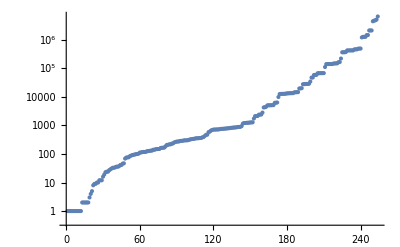

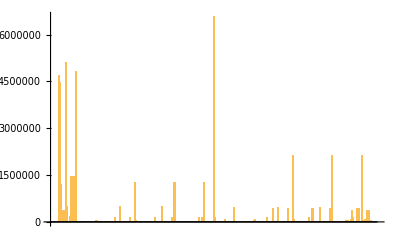

It also formats the truth tables that weren’t generated into an array plot and lists the equivalent expressions for each of those truth tables.

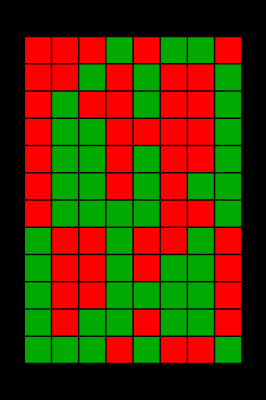

Xor[a,b,c,And[a,b,c]]
Not[Xor[a,b,c,And[a,b],And[a,b,c]]]
Not[Xor[a,b,c,And[a,c],And[a,b,c]]]
Not[Xor[a,b,c,And[b,c],And[a,b,c]]]
Not[Xor[a,b,c]]
Not[Xor[a,b,And[a,c],And[b,c],And[a,b,c]]]
Not[Xor[b,c,And[a,b],And[a,c],And[a,b,c]]]
Xor[a,c,And[a,b],And[b,c],And[a,b,c]]
Xor[a,b,c]
Xor[a,b,c,And[b,c],And[a,b,c]]
Xor[a,b,c,And[a,c],And[a,b,c]]
Not[Xor[a,b,c,And[a,b,c]]]

### Conclusion

From random generation I was able to deduce to a reasonable degree of certainty that it is impossible to generate an equivalent NAND expression that’s simpler than the one the Wolfram Language generates for three input XOR gates. There are most likely equivalent expressions out there for four or more input XOR expressions but that proves to be very computationally intensive and time consuming. It is pretty interesting how some expressions require significantly more NAND gates to be expressed because of their structure and the nature of NAND gates. It would be interesting to look into making expressions with NOR and XOR gates in the future and maybe putting more time into generating random expressions.